```mathematica
Remove["Global`*"]
```

```mathematica
m1=1;m2=2;l1=1;l2=2;th10=Pi/4;th20=Pi/3;g=9.8;dth10 = 0;dth20 = 0
```

0

```mathematica
Needs["VariationalMethods`"]
```

```mathematica
ELeqn =EulerEquations[1/2*m1*l1^2*th1'[t]^2+1/2*m2*(l1^2*th1'[t]^2+l2^2*th2'[t]^2+2*l1*l2*th1'[t]*th2'[t]*Cos[th1[t]-th2[t]])+m1*g*l1*Cos[th1[t]]+m2*g*(l1*Cos[th1[t]]+l2*Cos[th2[t]]),{th1[t],th2[t]},t]
```

{-29.4 Sin[th1[t]]-4. Sin[th1[t]-th2[t]] th2'[t]^2-3. th1''[t]-4. Cos[th1[t]-th2[t]] th2''[t]==0,-39.2 Sin[th2[t]]+4. Sin[th1[t]-th2[t]] th1'[t]^2-4. Cos[th1[t]-th2[t]] th1''[t]-8. th2''[t]==0}

```mathematica
Soln = NDSolve[{ELeqn,
th1[0]==th10,
th2[0]==th20,
th1'[0]==dth10,
th2'[0]==dth20},{th1,th2},{t,0,5}]
```

{{th1→InterpolatingFunction[{{0., 5.}}, <>],th2→InterpolatingFunction[{{0., 5.}}, <>]}}

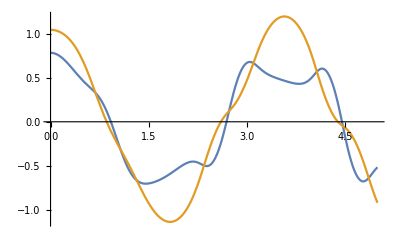

```mathematica
Subscript[θ, 1][t_]:=Evaluate[th1[t]/.First[Soln]];Subscript[θ, 2][t_]:=Evaluate[th2[t]/.First[Soln]];
Plot[{Subscript[θ, 1][t],Subscript[θ, 2][t]},{t,0,5}]
```

```mathematica
P1[t_]:={l1*Sin[Subscript[θ, 1][t]],-l1*Cos[Subscript[θ, 1][t]]}
P2[t_]:={l1*Sin[Subscript[θ, 1][t]]+l2*Sin[Subscript[θ, 2][t]],-l1*Cos[Subscript[θ, 1][t]]-l2*Cos[Subscript[θ, 2][t]]}
```

```mathematica
Animate[ListPlot[{{0,0},P1[t],P2[t]},Joined->True,PlotRange->{{-3,3},{-3.5,0}},PlotMarkers->Graphics[{Blue,Thick,Disk[]},ImageSize->20], AspectRatio->Automatic,ImageSize->Large],{t,0,5}]
```

```mathematica
Animation = Table[ListPlot[{{0,0},P1[t],P2[t]},Joined->True,PlotRange->{{-3,3},{-3.5,0}},PlotMarkers->Graphics[{Blue,Thick,Disk[]},ImageSize->20], AspectRatio->Automatic,ImageSize->Large],{t,0,5,.1}];
```

```mathematica
Export["Double Pendulum.avi",Animation,"DisplayDurations"->0.1]
```

Double Pendulum.avi

```mathematica
SystemOpen["Double Pendulum.avi"]
```